## 展开和变换

预备工作：

```mathematica
imgSize=300;
```

### 级数

#### 情形一

我们常常使用级数。那么级数如何形象的去理解呢？

举个例子说明，比如我们有一个这样的数列：

2,1/2,4/3,3/4,...,(n+(-1)^(n-1))/n,...

我们可以把这些数画在一个坐标系中。例如我们有这样一个数列：

```mathematica
exampleSeries=(n+(-1)^(n-1))/n;
```

数列的前几项是：

```mathematica
Append[Table[exampleSeries,{n,1,10}],"..."]
```

{2,1/2,4/3,3/4,6/5,5/6,8/7,7/8,10/9,9/10,...}

我们可以把各项在图上表示出来。其中

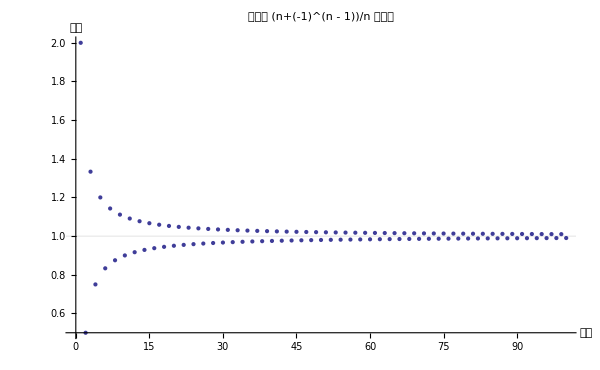
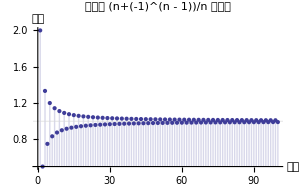
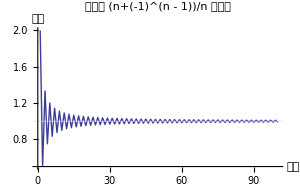

```mathematica
example1=Table[exampleSeries,{n,1,100}];
Grid[{
{ListPlot[example1,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example1,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->imgSize]
ListPlot[example1,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->imgSize]}
}]
```

从这个图中看到这个数列的极限通项大概是越来越接近 1 的。那么它的极限到底是不是 1 呢？

```mathematica
Limit[exampleSeries,n->Infinity]
```

1

确实是 1 。

#### 情形二

另一种情形是这样的。

```mathematica
Table[1/Log[n],{n,2,10}]
```

{1/Log[2],1/Log[3],1/Log[4],1/Log[5],1/Log[6],1/Log[7],1/Log[8],1/Log[9],1/Log[10]}

```mathematica
Sum[1/Log[n],{n,2,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=2)^∞ 1/Log[n]